```mathematica
toGraphicsRow[xs_List] :=( Graphics[{#, EdgeForm[{Thin, Black}], Rectangle[]}])& /@xs//GraphicsRow
```

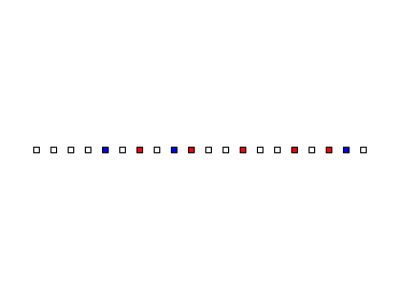

```mathematica
toGraphicsRow[Table[RandomChoice[{Red, White, Blue}], 20]]
```

```mathematica
swap[xs_List,p_,q_]:=Permute[xs, Cycles[{{p, q}}]]
```

```mathematica
dutchFlag[{xs_List, r_Integer, w_Integer, b_Integer}] := Switch[xs[[w+1]], White, {xs, r, w+1, b}, Red, {swap[xs, r+1, w+1], r+1, w+1, b}, Blue, {swap[xs, w+1, b], r, w, b-1}]
```

```mathematica
bxs = Table[RandomChoice[{Red, White, Blue}], 50]
```

{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0]}

```mathematica
dutchNotDone[tpl_List] := tpl[[3]] < tpl[[4]]
```

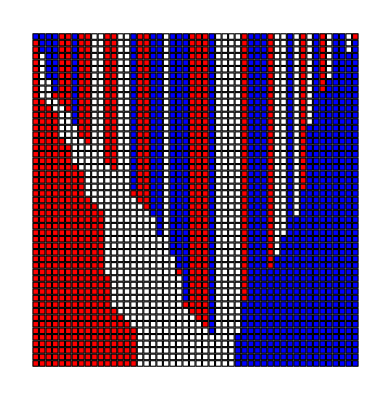

```mathematica
( Graphics[{#, EdgeForm[{Thin, Black}], Rectangle[]}])& /@ (#[[1]])& /@ NestWhileList[dutchFlag, {bxs, 0, 0, 50}, dutchNotDone] // GraphicsGrid
```

```mathematica
bxs2 = Table[RandomChoice[{Red, White, Blue}], 10]
```

{GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1]}

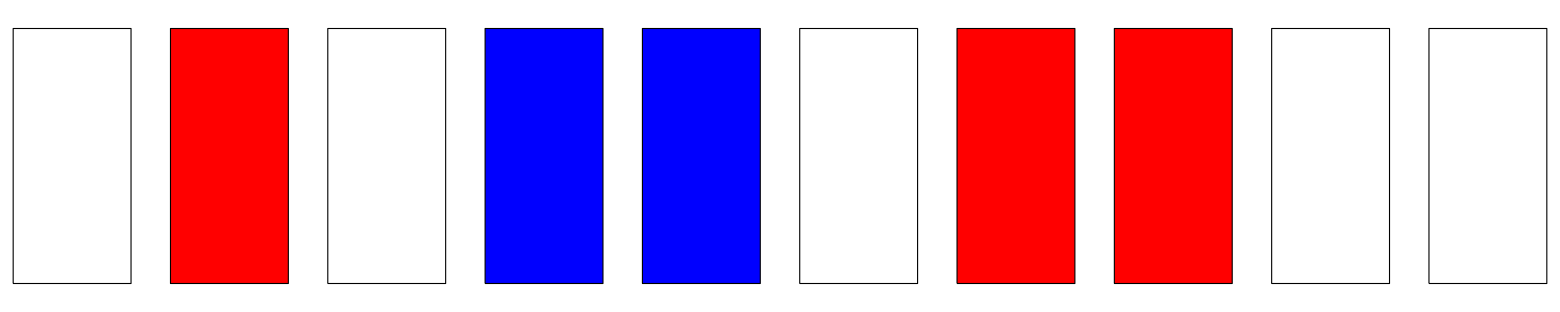

```mathematica
toGraphicsRow[bxs2]
```

```mathematica
dutchFlag[{bxs2, 0, 0, 10}]
```

{{GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1]},0,1,10}

```mathematica
toGraphicsRow[dutchFlag[{bxs2, 0, 0, 10}][[1]]]
```

-Graphics-

```mathematica
Nest[dutchFlag, {bxs2, 0, 0, 10}, 10]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},3,8,8}

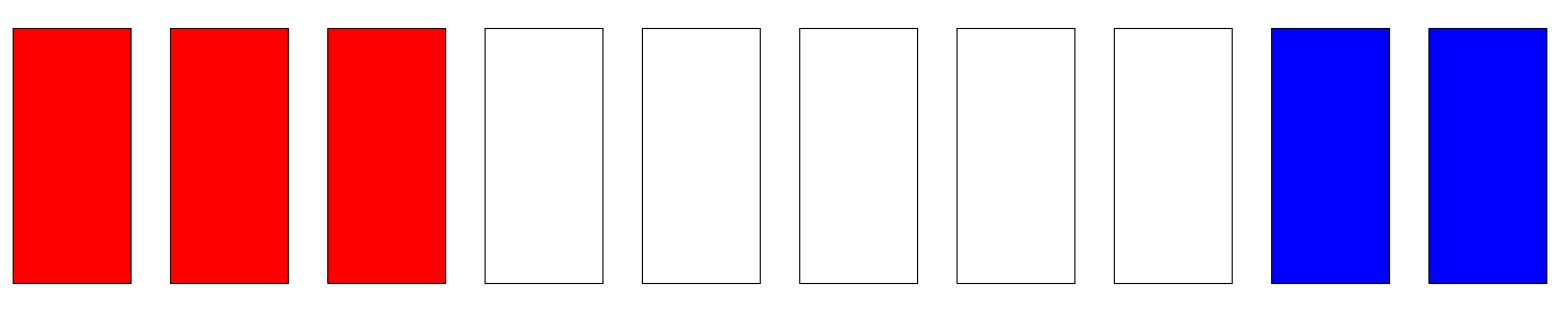

```mathematica
toGraphicsRow[Nest[dutchFlag, {bxs2, 0, 0, 10}, 10][[1]]]
```

```mathematica
NestWhileList[dutchFlag, {bxs, 0, 0, 50}, dutchNotDone]
```

{{{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0]},0,0,50},{{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1]},0,0,49},{{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1]},1,1,49},{{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,1,48},{{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,2,48},{{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,2,47},{{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,2,46},{{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,2,45},{{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,3,45},{{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},1,3,44},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},2,4,44},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},3,5,44},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},4,6,44},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},4,6,43},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},4,6,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},4,7,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},5,8,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},6,9,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},6,10,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},6,11,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},7,12,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},8,13,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},8,14,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},8,15,42},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},8,15,41},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},9,16,41},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},10,17,41},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,18,41},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,18,40},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,19,40},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,19,39},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,19,38},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,20,38},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,21,38},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,21,37},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,22,37},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},11,22,36},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},12,23,36},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},12,23,35},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},12,23,34},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},12,23,33},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},12,23,32},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},13,24,32},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},14,25,32},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},15,26,32},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,27,32},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,27,31},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,28,31},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,29,31},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,30,31},{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},16,31,31}}